```mathematica
data=Import["H:\\out.txt","Data"];
```

```mathematica
f1=Interpolation[data,Method->"Piecewise"];
f1n=NIntegrate[f1[x],{x,0,10}];
f1d=Table[{NIntegrate[f1[x]/f1n,{x,0,j^5}],j^5},{j,0,6.6^(1/5),0.01}]~Join~{{1,10}};
f2=Interpolation[f1d];
```

```mathematica
test=Table[f2[Random[]],{i,10000}];
```

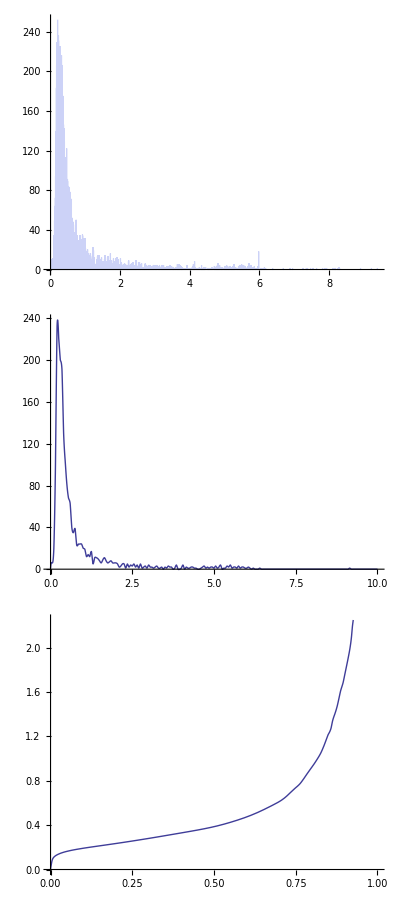

```mathematica
Column@{Histogram[test,1000,ImageSize->500],Plot[f1[x],{x,0,10},PlotRange->Full,ImageSize->500],Plot[f2[x],{x,0,1},ImageSize->500]}
```